## |+><+| State

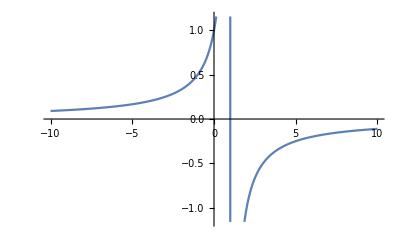

```mathematica
ρ={{1/2,1/2},{1/2,1/2}};
ζ[u_]:=Det[IdentityMatrix[2]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10}]
```

```mathematica
Manipulate[Plot[Abs[ζ[x+y I]],{y,-10,10},PlotRange->{0,1}],{x,-100,100}]
```

```mathematica
Solve[ζ[u]==0,u]
```

{}

## |00><00| State

```mathematica
ρ={{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
ζ[u_]:=Det[IdentityMatrix[4]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10}]
```

-Graphics-

## Maximally Mixed States

```mathematica
maxMix=Table[1/2^n IdentityMatrix[2^n],{n,1,5}];
```

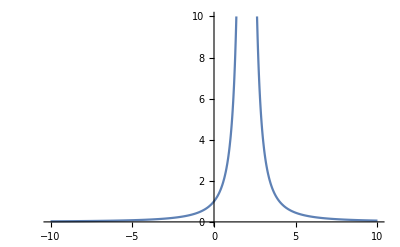

```mathematica
ζ[u_]:=Det[IdentityMatrix[2]-u*maxMix[[1]]]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{0,10}]
```

```mathematica
Manipulate[Plot[Abs[ζ[x+y I]],{y,-10,10},PlotRange->{0,1}],{x,-10,10}]
```

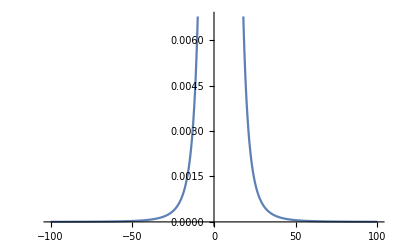

```mathematica
ζ[u_]:=Det[IdentityMatrix[4]-u*maxMix[[2]]]^(-1)
Plot[ζ[u],{u,-100,100}]
```

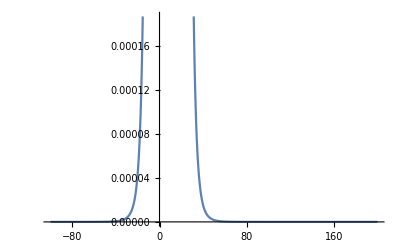

```mathematica
ζ[u_]:=Det[IdentityMatrix[8]-u*maxMix[[3]]]^(-1)
Plot[ζ[u],{u,-100,200}]
```

## Isotropic State (2 qubit)

```mathematica
Clear[ρ]
```

```mathematica
ρ[p_]:={{p/4+(1-p)/2, 0, 0, (1-p)/2}, {0, p/4, 0, 0}, {0, 0, p/4, 0}, {(1-p)/2, 0, 0, p/4+(1-p)/2}};
ζ[u_,p_]:=Det[IdentityMatrix[4]-u*ρ[p]]^(-1)
Plot3D[ζ[u,p],{u,-100,100},{p,0,1},AxesLabel->Automatic,PlotRange->{-5,5}]
Eigenvalues[ρ[p]]
```

-Graphics3D-

{1/4 (4-3 p),p/4,p/4,p/4}

### Maximally Mixed On Two Qubits

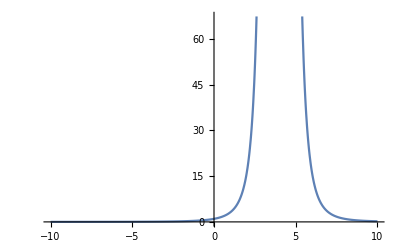

```mathematica
Plot[ζ[u,1],{u,-10,10}]
```

### Maximally Entangled On Two Qubits

```mathematica
Plot[ζ[u,0],{u,-10,10}]
```

-Graphics-

### Halfway Between Maximally Mixed and Maximally Entangled

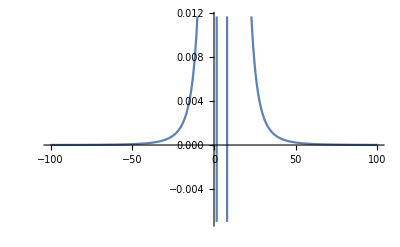

```mathematica
Plot[ζ[u,1/2],{u,-100,100}]
```

### Manipulate the isotropic parameter (extra pole comes from infinity and recombines with first pole)

```mathematica
m=Manipulate[Plot[ζ[u,p],{u,-10,50},PlotRange->{-3,3}],{p,0,1}]
```

```mathematica
Export["isotropicstate2.avi",m]
```

isotropicstate2.avi

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["isotropicstate2.avi"]]]
```

```mathematica
SystemOpen["isotropicstate.avi"]
```

## Isotropic State (3 qubit)

```mathematica
Clear[ρ]
```

```mathematica
ρ[p_]:={{p/8+(1-p)/2, 0, 0, 0, 0, 0, 0, p/8+(1-p)/2}, {0, p/8, 0, 0, 0, 0, 0, 0}, {0, 0, p/8, 0, 0, 0, 0, 0}, {0, 0, 0, p/8, 0, 0, 0, 0}, {0, 0, 0, 0, p/8, 0, 0, 0}, {0, 0, 0, 0, 0, p/8, 0, 0}, {0, 0, 0, 0, 0, 0, p/8, 0}, {p/8+(1-p)/2, 0, 0, 0, 0, 0, 0, p/8+(1-p)/2}};
ζ[u_,p_]:=Det[IdentityMatrix[8]-u*ρ[p]]^(-1)
Plot3D[ζ[u,p],{u,-100,100},{p,0,1},AxesLabel->Automatic,PlotRange->{-5,5}]
```

-Graphics3D-

### Maximally Mixed On Three Qubits

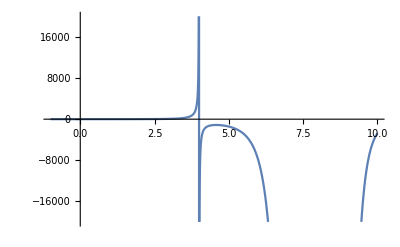

```mathematica
Plot[ζ[u,1],{u,-1,10},PlotRange->{-20000,20000}]
```

```mathematica
Solve[1/ζ[u,1]==0,u]
```

{{u→4},{u→8},{u→8},{u→8},{u→8},{u→8},{u→8}}

### Maximally Entangled On Three Qubits

```mathematica
Plot[ζ[u,0],{u,-10,10}]
```

-Graphics-

### Halfway Between Maximally Mixed and Maximally Entangled

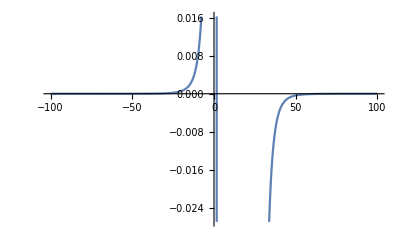

```mathematica
Plot[ζ[u,1/2],{u,-100,100}]
```

```mathematica
Solve[1/ζ[u,1/2]==0,u]
```

{{u→8/5},{u→16},{u→16},{u→16},{u→16},{u→16},{u→16}}

```mathematica
Manipulate[Solve[1/ζ[u,p]==0,u],{p,0,1}]
```

### Manipulate the isotropic parameter (extra pole comes from infinity and recombines with first pole)

```mathematica
Manipulate[Plot[ζ[u,p],{u,-100,100}],{p,0,1}]
```

## Weakly Entangled State

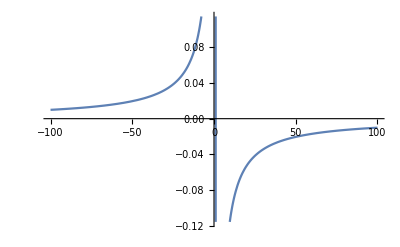

```mathematica
ρ={{1/6, 1/6, 1/6, 1/Sqrt[12]}, {1/6, 1/6, 1/6, 1/√12}, {1/6, 1/6, 1/6, 1/√12}, {1/√12, 1/√12, 1/√12, 1/2}};
ζ[u_]:=Det[IdentityMatrix[4]-u*ρ]^(-1)
Plot[ζ[u],{u,-100,100}]
```

### Weakly Entangled State’s Reduced State (Trace out first part)

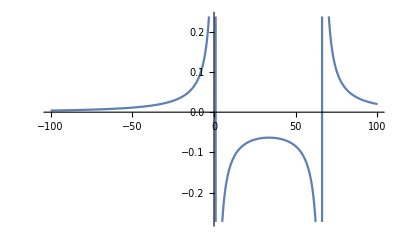

```mathematica
ρ={{1/3,1/6+1/√12},{1/6+1/√12,2/3}};
ζ[u_]:=Det[IdentityMatrix[2]-u*ρ]^(-1)
Plot[ζ[u],{u,-100,100}]
```

```mathematica
Solve[1/ζ[u]==0,u]
```

{{u→(3 (-3-√(5+2 √3)))/(-2+√3)},{u→(3 (-3+√(5+2 √3)))/(-2+√3)}}

```mathematica
Integrate[ζ[u],{u,(3 (-3-√(5+2 √3)))/(-2+√3),Infinity}]
```

∞

```mathematica
Manipulate[Plot[Abs[ζ[x+y I]],{y,-10,10},PlotRange->{0,1}],{x,-10,80}]
```

## W State

```mathematica
ρ=1/3{{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}};
ζ[u_]:=Det[IdentityMatrix[8]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10}]
```

-Graphics-

### W State Reduced (traced out first system)

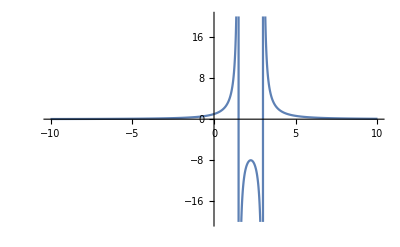

```mathematica
ρ=1/3{{1, 0, 0, 0}, {0, 1, 1, 0}, {0, 1, 1, 0}, {0, 0, 0, 0}};
ζ[u_]:=Det[IdentityMatrix[4]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{-20,20}]
```

```mathematica
Solve[1/ζ[u]==0,u]
```

{{u→3/2},{u→3}}

### W State Reduced (trace out first two systems)

```mathematica
ρ=1/3{{2, 0}, {0, 1}};
ζ[u_]:=Det[IdentityMatrix[2]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{-20,20}]
```

-Graphics-

```mathematica
Solve[1/ζ[u]==0,u]
```

{{u→3/2},{u→3}}

## GHZ State

```mathematica
ρ=1/2{{1, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 1}};
ζ[u_]:=Det[IdentityMatrix[8]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10}]
```

-Graphics-

### GHZ State Reduced (trace out any system)

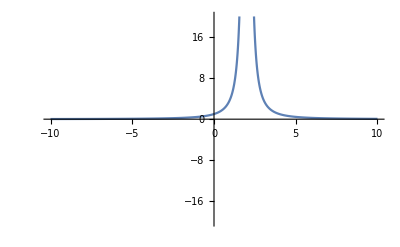

```mathematica
ρ=1/2{{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}};
ζ[u_]:=Det[IdentityMatrix[4]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{-20,20}]
```

```mathematica
Solve[1/ζ[u]==0,u]
```

{{u→2},{u→2}}

## Separable Mixed State (|00><00|+|11><11|)/2

```mathematica
ρ={{1/3, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 2/3}};
ζ[u_]:=Det[IdentityMatrix[4]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{-20,20}]
Solve[1/ζ[u]==0,u]
```

-Graphics-

{{u→3/2},{u→3}}

### Reduction of this state by tracing out first component

```mathematica
ρ={{1/3, 0}, {0, 2/3}};
ζ[u_]:=Det[IdentityMatrix[2]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{-20,20}]
Solve[1/ζ[u]==0,u]
```

-Graphics-

{{u→3/2},{u→3}}

### Kronecker Product

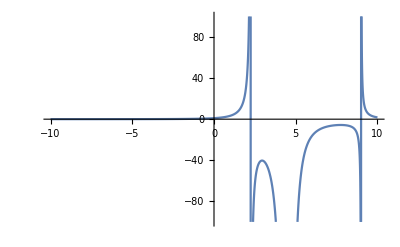

{{u→9/4},{u→9/2},{u→9/2},{u→9}}

```mathematica
σ={{1/3, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 2/3}};
ρ=KroneckerProduct[σ,σ];
ζ[u_]:=Det[IdentityMatrix[16]-u*ρ]^(-1)
Plot[ζ[u],{u,-10,10},PlotRange->{-100,100}]
Solve[1/ζ[u]==0,u]
```

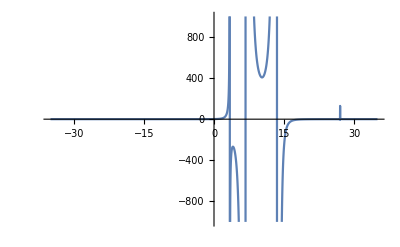

{{u→27/8},{u→27/4},{u→27/4},{u→27/4},{u→27/2},{u→27/2},{u→27/2},{u→27}}

```mathematica
σ={{1/3, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 2/3}};
ρ=KroneckerProduct[σ,σ,σ];
ζ[u_]:=Det[IdentityMatrix[64]-u*ρ]^(-1)
Plot[ζ[u],{u,-35,35},PlotRange->{-1000,1000}]
Solve[1/ζ[u]==0,u]
```

## If algorithm is extendible to mixed states, then cycle index is not the acceptance prob.

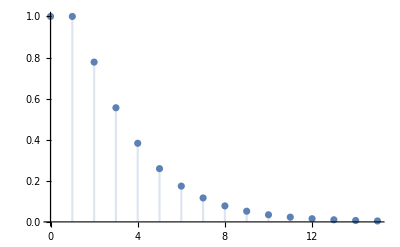

```mathematica
DiscretePlot[D[ζ[u],{u,n}]/n!/.{u->0},{n,0,15}]
```